```mathematica
a=3;
b=3;

P[x_]=x^(a-1)*Exp[-b*x]*b^a/Gamma[a];

PL[s_]=LaplaceTransform[P[x],x,s];
```

ⅇ^(∑_(n=1)^N ((-1)^(2 n) s^n PL^(n)[0])/(n!))

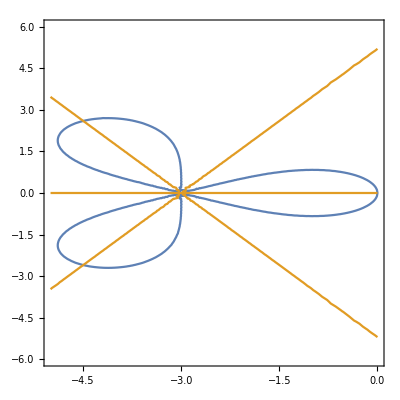

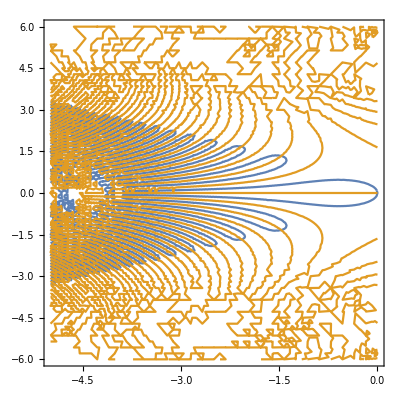

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

NIntegrate::inumr: The integrand 2 ⅇ^(200 (1-ⅇ^Times[«2»])-2 (-1+t)+(-a-ⅈ b) t) (1-ⅇ^((1-t)/100)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,1.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {76.4272}. NIntegrate obtained -0.384766+0.418457 ⅈ and 5.00008 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {76.4272}. NIntegrate obtained -0.384766+0.418457 ⅈ and 5.00008 for the integral and error estimates.

```mathematica
K[n_]=(-1)^n Derivative[n][PL][0];

polynome[s_,N_]=Exp[Sum[(-1)^n*K[n]*s^n/Factorial[n],{n,1,N}]]

ll=u+I*v;


PLplot=PL[ll];
test10=polynome[ll,3];






ContourPlot[{Re[PLplot]==1,Im[PLplot]==0},{u,-5,0},{v,-6,6}]

ContourPlot[{Re[test10]==1,Im[test10]==0},{u,-5,0},{v,-6,6}]




Plot3D[{Re[test10],Re[PLplot]},{u,-5,0},{v,-6,6}]
Plot3D[{Re[test10]},{u,-5,0},{v,-6,6}]
Plot3D[Re[PLplot],{u,-5,0},{v,-6,6}]

Plot3D[{Im[test10],Im[PLplot]},{u,-5,0},{v,-6,6}]
```